```mathematica
NS[]
```

```mathematica
nmix[a_,m_,s_]=TransformedDistribution[{q1,q2,1-q1-q2}.{m1,m2,m3},{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}/3],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s],m4\[Distributed]NormalDistribution[m,s]}]
```

TransformedDistribution[m1 q1+m3 (1-q1-q2)+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]ProductDistribution[DirichletDistribution[{a/3,a/3,a/3}],NormalDistribution[m,s],NormalDistribution[m,s],NormalDistribution[m,s]]]

```mathematica
FS@Mean[nmix[a,m,s]]
```

m

```mathematica
FS@CentralMoment[nmix[a,m,s],2]
```

((3+a) s^2)/(3 (1+a))

```mathematica
FS@CentralMoment[nmix[a,m,s],3]
```

0

```mathematica
dp[x_,a_,m_,s_]=PDF[nmix[a,m,s],x]
```

PDF[TransformedDistribution[m1 q1+m3 (1-q1-q2)+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]ProductDistribution[DirichletDistribution[{a/3,a/3,a/3}],NormalDistribution[m,s],NormalDistribution[m,s],NormalDistribution[m,s]]],x]

```mathematica
dp[2,4,0,1]
```

PDF[TransformedDistribution[m1 q1+m3 (1-q1-q2)+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]ProductDistribution[DirichletDistribution[{4/3,4/3,4/3}],NormalDistribution[0,1],NormalDistribution[0,1],NormalDistribution[0,1]]],2]

```mathematica
Assuming[assu&&x>0,PDF[ParameterMixtureDistribution[InverseGammaDistribution[a,k],k\[Distributed]GammaDistribution[a2,b2]],x]]
```

(b2^a x^(-1+a2) (b2+x)^(-a-a2) Gamma[a+a2])/(Gamma[a] Gamma[a2])

```mathematica
{dgamma[x_,a_]=Assuming[a>0&&x>0,FS@PDF[GammaDistribution[a,1],x]],
dnorm[x_,m_,s_]=Assuming[s>0,FS@PDF[NormalDistribution[m,s],x]],
digg[x_,a_,b2_]=Assuming[a>0&&x2>0&&x>0,FS@PDF[TransformedDistribution[Sqrt[v],v\[Distributed]ParameterMixtureDistribution[InverseGammaDistribution[a,k],k\[Distributed]GammaDistribution[a,b2]]],x]]}
```

{(ⅇ^-x x^(-1+a))/Gamma[a],(ⅇ^(-(m-x)^2/(2 s^2)))/(√(2 π) s),(2 b2^a (b2/x+x)^(-2 a) Gamma[2 a])/(x Gamma[a]^2)}

```mathematica
apprd[x_,a_,m_,s_]:=NIntegrate[(q1*dnorm[x,m,s]+q2*dnorm[x,m,s]+q3*dnorm[x,m,s])/(q1+q2+q3)*dgamma[q1,a]*dgamma[q2,a]*dgamma[q3,a],{q1,0,+Infinity},{q2,0,+Infinity},{q3,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

```mathematica
apprd[2,4,0,1]
```

0.054035

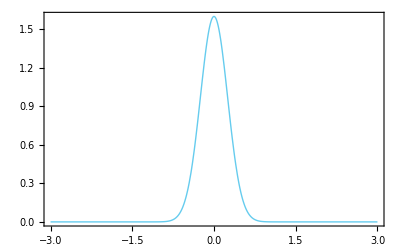

```mathematica
Plot[apprd[x,4,0,1/4],{x,-3,3},PlotRange->{0,All}]
```

```mathematica
apprdh[x_,a_,s0_,m1_,s1_]:=NIntegrate[(q1*dnorm[x,m,s]+q2*dnorm[x,m,s]+q3*dnorm[x,m,s])/(q1+q2+q3)*dgamma[q1,a]*dgamma[q2,a]*dgamma[q3,a]*dnorm[m,0,s0]*digg[s,m1,s1],{q1,0,+Infinity},{q2,0,+Infinity},{q3,0,+Infinity},{m,-Infinity,+Infinity},{s,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

```mathematica
apprdh[{-3,-2,-1,0,1,2,3},4,1,1,1]
```

{0.0360289,0.092693,0.199196,0.266306,0.199196,0.092693,0.0360289}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.39346×10^18 and 9.88481×10^17 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.39346×10^18 and 9.88481×10^17 for the integral and error estimates.

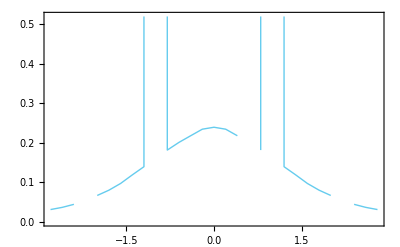

```mathematica
xgrid=Table[i,{i,-3,3,0.2}];
ListPlot[T@{xgrid,apprdh[xgrid,4,1,1/4,1]},Joined->True]
```

```mathematica
dinorm[x_,m_,s_]=Integrate[dnorm[y,m,s],{y,-Infinity,x},Assumptions->{s>0,m∈Reals}]
```

1/2 Erfc[(m-x)/(√2 s)]

```mathematica
cdh[x_,a_,s0_,m1_,s1_]:=NIntegrate[(q1*dinorm[x,m,s]+q2*dinorm[x,m,s]+q3*dinorm[x,m,s])/(q1+q2+q3)*dgamma[q1,a]*dgamma[q2,a]*dgamma[q3,a]*dnorm[m,0,s0]*digg[s,m1,s1],{m,-Infinity,+Infinity},{s,0,+Infinity},{q1,0,+Infinity},{q2,0,+Infinity},{q3,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

```mathematica
cdh[2,4,0,1,1]
```

0.922027

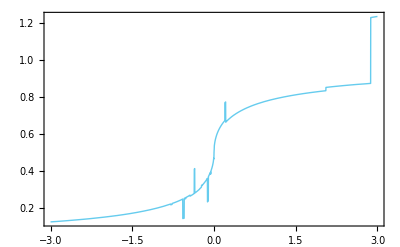

```mathematica
Plot[cdh[x,4,0,1/4,1],{x,-3,3},PlotRange->{0,All}]
```

```mathematica
Plot[dp[x,4,0,1],{x,-3,3}]
```

$Aborted

```mathematica
Quantile[nmix[4.,0.,1.],0.25]
```

Quantile[TransformedDistribution[m1 q1+m3 (1-q1-q2)+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]ProductDistribution[DirichletDistribution[{1.33333,1.33333,1.33333}],NormalDistribution[0.,1.],NormalDistribution[0.,1.],NormalDistribution[0.,1.]]],0.25]

```mathematica
dp[x_,a_,m_,s_]:=PDF[
```

```mathematica
Plot[InverseCDF[nmix[4,0,x],1/4],{x,1,2}]
```

-Graphics-

```mathematica
FindRoot[{InverseCDF[nmix[a,0,s],0.25]==1,
InverseCDF[nmix[a,0,s],0.125]==2},{{a,1},{m,0},{s,1}}]
```

FindRoot::nlnum: The function value {-1.+InverseCDF[TransformedDistribution[m1 q1+m3 (1.+Times[«2»]+Times[«2»])+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]«1»],0.25],-2.+InverseCDF[TransformedDistribution[m1 q1+m3 (1.+Times[«2»]+Times[«2»])+m2 q2,{«1»}\[Distributed]«1»],«6»]} is not a list of numbers with dimensions {2} at {a,m,s} = {1.,0.,1.}.

FindRoot[{InverseCDF[nmix[a,0,s],0.25]==1,InverseCDF[nmix[a,0,s],0.125]==2},{{a,1},{m,0},{s,1}}]

```mathematica
FA[x_]:=Assuming[a>0&&a2>0&&b2>0,FS[x]]
```

```mathematica
dg[a_,a2_,b2_]=Assuming[assu,FS@ParameterMixtureDistribution[InverseGammaDistribution[a,k],k\[Distributed]GammaDistribution[a2,b2]]]
```

ParameterMixtureDistribution[InverseGammaDistribution[a,k],k\[Distributed]GammaDistribution[a2,b2]]

```mathematica
ldg[a_,a2_,b2_]=FA[TransformedDistribution[Log[y]/2,y\[Distributed]dg[a,a2,b2]]]
```

TransformedDistribution[Log[x]/2,x\[Distributed]ParameterMixtureDistribution[InverseGammaDistribution[a,k],k\[Distributed]GammaDistribution[a2,b2]]]

```mathematica
FA@Mean[ldg[a,a2,b2]]
```

1/2 (Log[b2]-PolyGamma[0,a]+PolyGamma[0,a2])

```mathematica
FA@CentralMoment[ldg[a,a,b2],3]
```

0

```mathematica
sdldg[a_]=FA@StandardDeviation[ldg[a,a,b2]]
```

(√PolyGamma[1,a])/(√2)

```mathematica
meanldg[b2_]=FA@Mean[ldg[a,a,b2]]
```

Log[b2]/2

```mathematica
Solve[{sdlgd[a]==ss,a>0,ss>0},a]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{sdlgd[a]==ss,a>0,ss>0},a]

```mathematica
FindRoot[PolyGamma[1,a]==ss,a]
```

FindRoot::fdss: Search specification a should be a list with 1 to 5 elements.

FindRoot[PolyGamma[1,a]==ss,a]